# Superposition of Spherical harmonic

```mathematica
Y[l_,m_]:=SphericalHarmonicY[l,m,θ,ϕ]//ComplexExpand
y[l_,m_]:=ComplexExpand[Conjugate[Y[l,m]]]
NY[l_,m_]:=Simplify[√(y[l,m]Y[l,m]),{Sin[θ]>0,Cos[θ]>0}]
```

```mathematica
NY[1,1]
NY[1,0]
NY[2,2]
NY[2,1]
NY[2,0]
```

1/2 √(3/(2 π)) Sin[θ]

1/2 √(3/π) Cos[θ]

1/4 √(15/(2 π)) Sin[θ]^2

1/4 √(15/(2 π)) Sin[2 θ]

1/4 √(5/π) Abs[1-3 Cos[θ]^2]

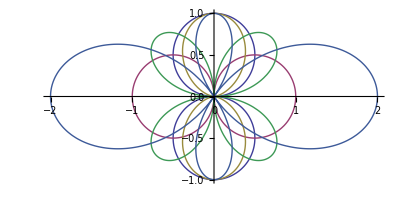

```mathematica
PolarPlot[{√(Sin[θ]^2),√(Cos[θ]^2),√(Sin[θ]^4),√(Sin[2 θ]^2),√((-1+3 Cos[θ]^2)^2)},{θ,0,2π}]
```

```mathematica
Y[1,1]
Y[2,2]
Y[2,0]
Y[3,3]
```

-1/2 √(3/(2 π)) Cos[ϕ] Sin[θ]-1/2 ⅈ √(3/(2 π)) Sin[θ] Sin[ϕ]

1/4 √(15/(2 π)) Cos[2 ϕ] Sin[θ]^2+1/4 ⅈ √(15/(2 π)) Sin[θ]^2 Sin[2 ϕ]

-(√(5/π))/4+3/4 √(5/π) Cos[θ]^2

-1/8 √(35/π) Cos[3 ϕ] Sin[θ]^3-1/8 ⅈ √(35/π) Sin[θ]^3 Sin[3 ϕ]

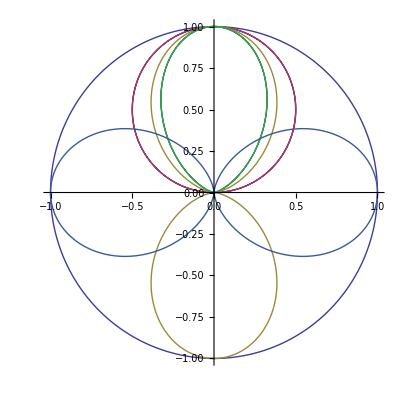

```mathematica
PolarPlot[{1,Sin[θ],Sin[θ]^2,Sin[θ]^3,Cos[θ]^2},{θ,0,2π}]
```

```mathematica
Manipulate[PolarPlot[{1,1+a Cos[n θ]},{θ,0,2π}],{{a,0.2},0.1,10},{n,1,10,1}]
```

```mathematica
Manipulate[SphericalPlot3D[{(1+a Cos[n θ])/(√(1+a^2))},{θ,0,2π},{ϕ,0,π}],{{a,0.2},0.1,10},{n,1,10,1}]
```